## Analysis of SimTree output

## Basic parameters

```mathematica
demeCount=3;
```

```mathematica
demes={"North","Tropics","South"};
```

```mathematica
clipStartTime=-10;
```

```mathematica
clipEndTime=100;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/SimTree/source

```mathematica
spatialColors={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

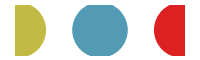

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,spatialColors]},AspectRatio->0.3,ImageSize->200]
```

```mathematica
spatialColorRules=MapIndexed[#2[[1]]-1->#1&,spatialColors];
```

```mathematica
trunkColors={GrayLevel[0.3],RGBColor[0.857,0.131,0.132]};
```

```mathematica
trunkColorRules=MapIndexed[#2[[1]]-1->#1&,trunkColors];
```

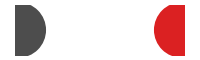

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,trunkColors]},AspectRatio->0.3,ImageSize->200]
```

## Loess fit

```mathematica
LoessFit[(x_)?VectorQ,data_,α_:0.75,λ_:1]:=Table[LoessFit[x[[i]],data,α,λ],{i,Length[x]}]
```

```mathematica
LoessFit[(x_)?NumberQ,data_,α_:0.75,λ_:1]:=WLSFit[data,LoessWts[x,data,α],λ,x];
```

```mathematica
WLSFit[data_,wts_,ldegree_:1,x_]:=Fit[Transpose[(wts*#1&)/@Join[{Table[1,{Length[data]}]},Transpose[data]]],Join[{u},Table[v^i,{i,ldegree}]],{u,v}]/.{u->1,v->x}
```

```mathematica
LoessWts[x_,data_,α_]:=Tricube[(x-First[Transpose[data]])/LoessDistance[x,data,α]]
```

```mathematica
Tricube=Compile[{{x,_Real,1}},If[Abs[#]<1,(1-Abs[#]^3)^3,0]&/@x];
```

```mathematica
LoessDistance[x_,data_,α_]:=Module[{A=Max[1,α],X=First[Transpose[data]],q},q=Min[Length[X],Ceiling[α*Length[X]]];A*Sort[Abs[X-x]][[q]]]
```

## Options

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

## Assumptions

### R0

5 day recovery

```mathematica
0.2*1.8
```

0.36

### Mutation

Let’s say there are 10 sites that function to move the virus in phenotype space

```mathematica
20*0.005*(1/365)
```

0.000273973

Mutations per day

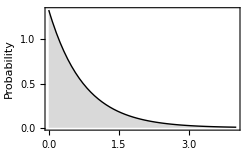

```mathematica
fig=Plot[PDF[ExponentialDistribution[1/0.75],x],{x,0,4},ImageSize->250,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"Antigenic distance","Probability"}]
```

```mathematica
CDF[ExponentialDistribution[2.],2]
```

0.981684

### Cross-immunity

The antigenic map is on a Log2 scale.

Average distance between clusters is 4.5 units.

Rough cross-immunity between clusters is 0.65 to 0.80.

4.5 units = 0.3 risk of infection

```mathematica
4.5*0.067
```

0.3015

```mathematica
TableForm[N[Table[x*0.067,{x,0,6}]],TableHeadings->{Range[0,6]}]
```

0 | 0.
1 | 0.067
2 | 0.134
3 | 0.201
4 | 0.268
5 | 0.335
6 | 0.402

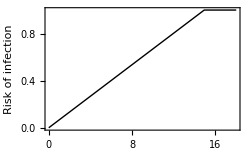

```mathematica
fig=Plot[Clip[x*0.067],{x,0,18},PlotStyle->Black,ImageSize->250,FrameLabel->{"Antigenic distance","Risk of infection"}]
```

## World-wide SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

40.

```mathematica
popSize=data[[1,3]]
```

1499980

```mathematica
Length[data]
```

14600

### Analysis window

```mathematica
data=Select[data,(#[[1]]>clipStartTime&&#[[1]]<clipEndTime&)];
```

### Yearly incidence

Mean incidence per year

```mathematica
N[(Total[inc[[All,2]]]/endTime)]
```

25525.7

```mathematica
N[(Total[inc[[All,2]]]/endTime)/popSize]
```

0.0170173

Flu incidence is 10% per year and prevalence is 0.14%.

### Pruning

```mathematica
data=data[[1;;-1;;10]];
```

### Prevalence

```mathematica
prev=data[[All,{1,5}]];
```

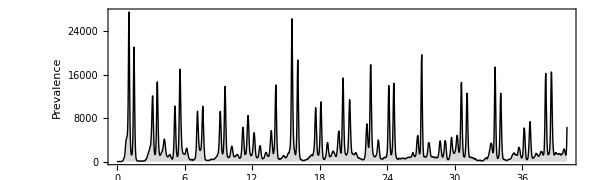

```mathematica
fig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]
```

```mathematica
Export["prevalence.pdf",fig,"PDF"]
```

prevalence.pdf

### Incidence

```mathematica
inc=data[[All,{1,7}]];
```

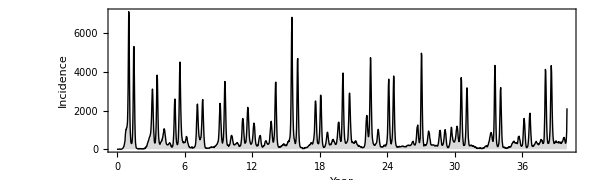

```mathematica
fig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"Year","Incidence"}]
```

```mathematica
Export["incidence.pdf",fig,"PDF"]
```

incidence.pdf

### Diversity

```mathematica
div=data[[All,{1,2}]];
```

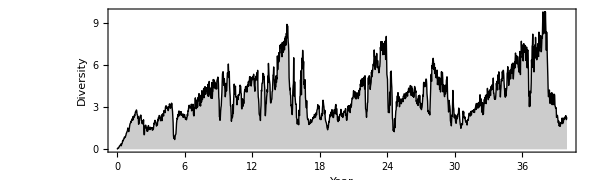

```mathematica
fig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"Year","Diversity"}]
```

```mathematica
Export["diversity.pdf",fig,"PDF"]
```

diversity.pdf

## Regional SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

40.

### Analysis window

```mathematica
data=Select[data,(#[[1]]>clipStartTime&&#[[1]]<clipEndTime&)];
```

### Yearly incidence

```mathematica
incList=Table[data[[All,i]],{i,12,12+(demeCount-1)*5,5}];
```

```mathematica
TableForm[N[Map[Total[#]&,incList]]/(endTime-startTime),TableHeadings->{demes}]
```

North | 90528.6
Tropics | 71928.5
South | 92965.8

```mathematica
table=TableForm[Round[Map[Total[#]&,incList]/((endTime-startTime)*(popSize/demeCount)),0.001],TableHeadings->{demes}]
```

North | 0.181
Tropics | 0.144
South | 0.186

### Pruning

```mathematica
data=data[[1;;-1;;10]];
```

### Prevalence

```mathematica
prevList=Table[data[[All,{1,i}]],{i,10,10+(demeCount-1)*5,5}];
```

```mathematica
max=Max[Map[Max,prevList]]
```

24275

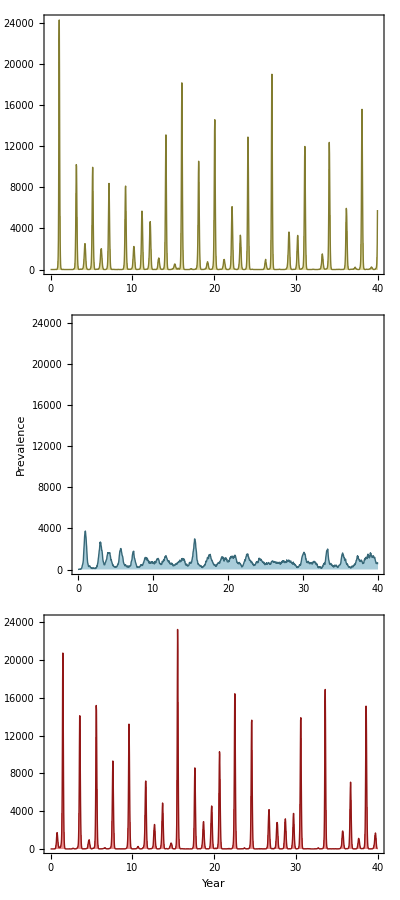

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Prevalence",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["prevalenceSpatial.pdf",fig,"PDF"]
```

prevalenceSpatial.pdf

## Tips

```mathematica
tipScale=0.001;
```

```mathematica
tipData=Import["out.tips","CSV"];
```

```mathematica
Length[tipData]
```

30227

```mathematica
traitHeader=tipData[[1]];
```

```mathematica
TableForm[traitHeader,TableHeadings->{Range[7]}]
```

1 | name
2 | year
3 | trunk
4 | location
5 | layout
6 | ag1
7 | ag1

```mathematica
tipData=Drop[tipData,1];
```

```mathematica
name=1;year=2;trunk=3;loc=4;layout=5;ag1=6;ag2=7;
```

### Analysis window

```mathematica
tipData=Select[tipData,(#[[year]]>clipStartTime&&#[[year]]<clipEndTime&)];
```

### Rotation

```mathematica
times=tipData[[All,year]];
```

```mathematica
pc=PrincipalComponents[tipData[[All,{ag1,ag2}]]];
```

```mathematica
first=pc[[First[Ordering[times]]]];
```

```mathematica
last=pc[[Last[Ordering[times]]]];
```

```mathematica
pc=If[first[[1]]>last[[1]],Map[{-#[[1]],#[[2]]}&,pc],pc];
```

```mathematica
tipData=MapThread[{#1[[name]],#1[[year]],#1[[trunk]],#1[[loc]],#1[[layout]],#2[[1]],#2[[2]]}&,{tipData,pc}];
```

```mathematica
startingPoint=If[first[[1]]>last[[1]],last,first];
```

```mathematica
dist[coord_]:=EuclideanDistance[startingPoint,coord]
```

### Graphics settings

```mathematica
frameWindow=1.0;
```

```mathematica
plotRange={{Floor[Min[tipData[[All,ag1]]],frameWindow],Ceiling[Max[tipData[[All,ag1]]],frameWindow]},{Floor[Min[tipData[[All,ag2]]],frameWindow],Ceiling[Max[tipData[[All,ag2]]],frameWindow]}}
```

{{-11.,11.},{-7.,9.}}

```mathematica
plotRange={{Floor[Quantile[tipData[[All,ag1]],0.01],frameWindow]-1,Ceiling[Quantile[tipData[[All,ag1]],0.99],frameWindow]+1},{Floor[Quantile[tipData[[All,ag2]],0.01],frameWindow]-1,Ceiling[Quantile[tipData[[All,ag2]],0.99],frameWindow]+1}}
```

{{-11.,11.},{-6.,7.}}

```mathematica
aspectRatio=Max[Apply[EuclideanDistance,plotRange[[2]]]/Apply[EuclideanDistance,plotRange[[1]]],0.15]
```

0.590909

```mathematica
imageSize=If[aspectRatio>1,600/aspectRatio,600]
```

600

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-100,100,frameWindow}],{2},{2}];
```

### Year vs AG1

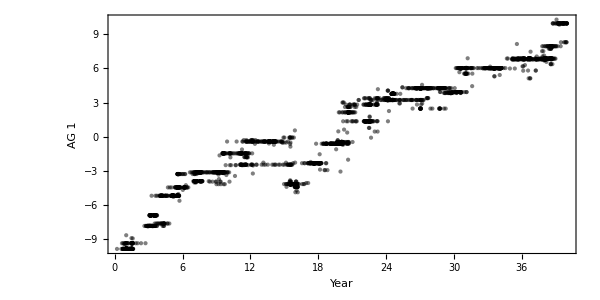

```mathematica
fig=ListPlot[RandomSample[tipData[[All,{year,ag1}]],3000],AspectRatio->0.5,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG1.pdf",fig,"PDF"]
```

tipsYearAG1.pdf

### Year vs AG2

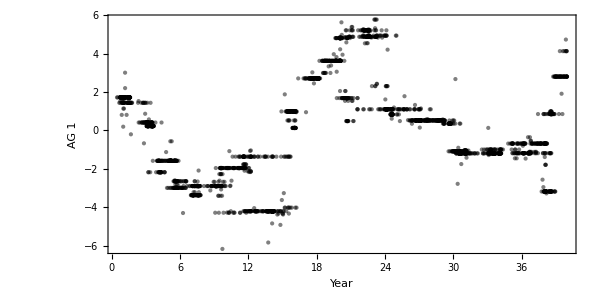

```mathematica
fig=ListPlot[RandomSample[tipData[[All,{year,ag2}]],3000],AspectRatio->0.5,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG2.pdf",fig,"PDF"]
```

tipsYearAG2.pdf

### AG1 vs AG2

```mathematica
tallies=Tally[tipData[[All,{ag1,ag2}]]];
```

```mathematica
points=Map[{PointSize[N[tipScale*Sqrt[#[[2]]]]],Point[#[[1]]]}&,tallies];
```

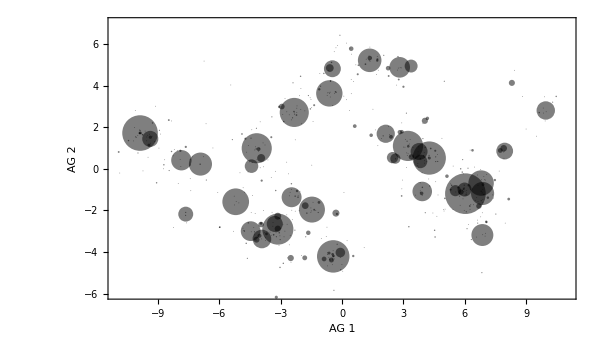

```mathematica
fig=Graphics[{Opacity[0.5],points},AspectRatio->aspectRatio,PlotRange->plotRange,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False}]
```

```mathematica
Export["tipsAG1AG2.pdf",fig,"PDF"]
```

tipsAG1AG2.pdf

### Map

Found average distance between two points of the same strain as 1.6 units

1.6 units is 1.6 * 0.067 = 0.11

```mathematica
spread=0.4;
```

```mathematica
test=Table[RandomVariate[NormalDistribution[0,spread],2],{100}];
```

```mathematica
Mean[Flatten[Table[EuclideanDistance[test[[i]],test[[j]]],{i,Length[test]},{j,i+1,Length[test]}]]]
```

0.700775

```mathematica
jitter=Flatten[Map[Table[#[[1]]+RandomVariate[NormalDistribution[0,spread],2],{Round[0.1*#[[2]]]}]&,tallies],1];
```

```mathematica
Length[jitter]
```

2959

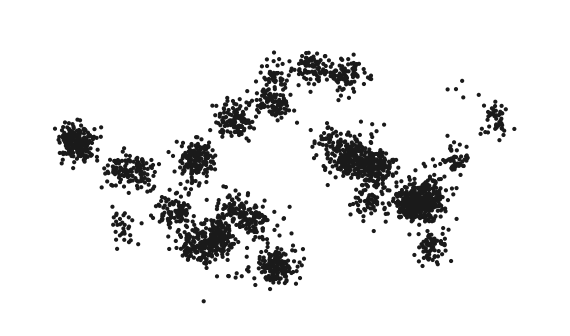

```mathematica
fig=ListPlot[jitter,AspectRatio->aspectRatio,PlotRange->plotRange,PlotStyle->GrayLevel[0.1],GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95]
```

```mathematica
Export["map.pdf",fig,"PDF"]
```

map.pdf

### Clustering

```mathematica
spread=0.4;
```

```mathematica
count=5000;
```

```mathematica
k=15;
```

```mathematica
step=0.1;
```

```mathematica
clusterColors=Table[ColorData["Rainbow"][i],{i,0,1,1/(k-1)}];
```

```mathematica
randomTips=RandomSample[tipData,count];
```

```mathematica
jitter=Map[#+RandomVariate[NormalDistribution[0,spread],2]&,randomTips[[All,{ag1,ag2}]]];
```

```mathematica
clustered=FindClusters[jitter->Range[count],k,Method->{"Agglomerate","Linkage"->"Average"}];
```

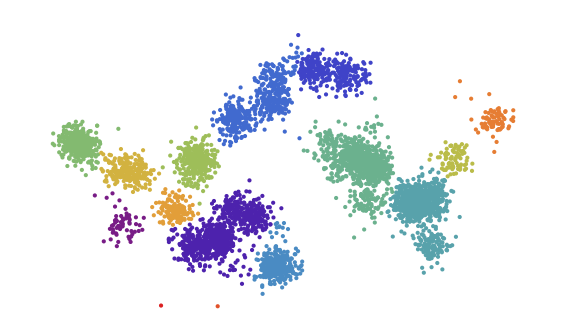

```mathematica
fig=ListPlot[Map[jitter[[#]]&,clustered],PlotStyle->clusterColors,AspectRatio->aspectRatio,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95]
```

```mathematica
Export["mapClusters.pdf",fig,"PDF"]
```

mapClusters.pdf

### Prevalence - clusters

```mathematica
times=randomTips[[All,year]];
```

```mathematica
pro=Table[Mean[Map[times[[#]]&,clustered][[i]]],{i,k}];
```

```mathematica
skls=Table[BinCounts[Map[times[[#]]&,clustered][[i]],{startTime,endTime,step}],{i,k}];
```

```mathematica
length=Length[skls[[1]]];
```

```mathematica
ord=Ordering[pro];
```

```mathematica
ordcolorlist=Map[clusterColors[[#]]&,ord];
```

```mathematica
skltable=Table[skls[[i]],{i, ord}];
```

```mathematica
timelist=Map[Mean,Partition[Range[startTime,endTime,step],2,1]];
```

```mathematica
skltable=MapIndexed[{timelist[[#2[[2]]]],#1}&,skltable,{2}];
```

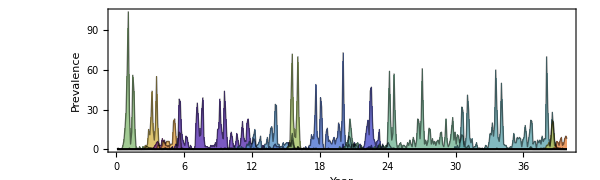

```mathematica
fig=ListLinePlot[skltable,Filling ->Table[i->{Axis,Directive[Opacity[0.75],ordcolorlist[[i]]]},{i,1,k}],PlotStyle->Directive[Opacity[0.5],Black],AspectRatio->0.3,PlotRangePadding->{{0.1,0},{0.05,0}},FrameLabel->{"Year","Prevalence"}]
```

```mathematica
Export["prevalenceClusters.pdf",fig,"PDF"]
```

prevalenceClusters.pdf

### Cluster function

```mathematica
clusterCenters=Map[Mean[jitter[[#]]]&,clustered]
```

{{-7.69165,-2.14742},{-2.96884,-2.57889},{2.12471,5.02114},{-1.31012,3.51908},{-0.348337,-4.11772},{6.38249,-1.35679},{3.59862,0.645607},{-9.74786,1.64636},{-4.19797,0.812615},{7.96868,0.921302},{-7.4018,0.337539},{-5.19495,-1.48423},{9.84314,2.7749},{-3.17854,-6.04452},{-5.85368,-6.01128}}

```mathematica
clusterFunction[p_]:=First[Nearest[clusterCenters->Range[k],p]]
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#]]],Point[#]}&,jitter];
```

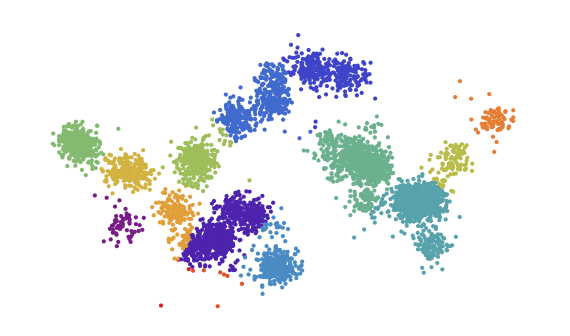

```mathematica
Graphics[points,AspectRatio->aspectRatio,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95]
```

### Distance from origin

```mathematica
list=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

AG change per year

```mathematica
(Max[list[[All,2]]]-Min[list[[All,2]]])/(endTime-startTime)
```

0.501098

Want 1.2 units per year

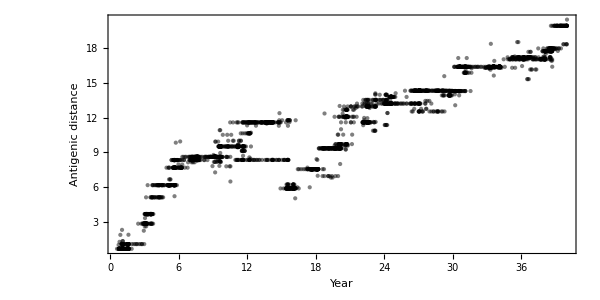

```mathematica
fig=ListPlot[RandomSample[list,3000],AspectRatio->0.5,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","Antigenic distance"}]
```

```mathematica
Export["tipsYearDistance.pdf",fig,"PDF"]
```

tipsYearDistance.pdf

### Loess spline

```mathematica
data=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

```mathematica
fit[x_]:=LoessFit[x,data,0.2,1]
```

```mathematica
startTime=Min[data[[All,1]]]
```

0.0904

```mathematica
endTime=Max[data[[All,1]]]
```

39.9973

```mathematica
max=Max[data[[All,2]]]
```

20.4453

```mathematica
loessList=Table[{x,fit[x]},{x,startTime,endTime,0.1}];
```

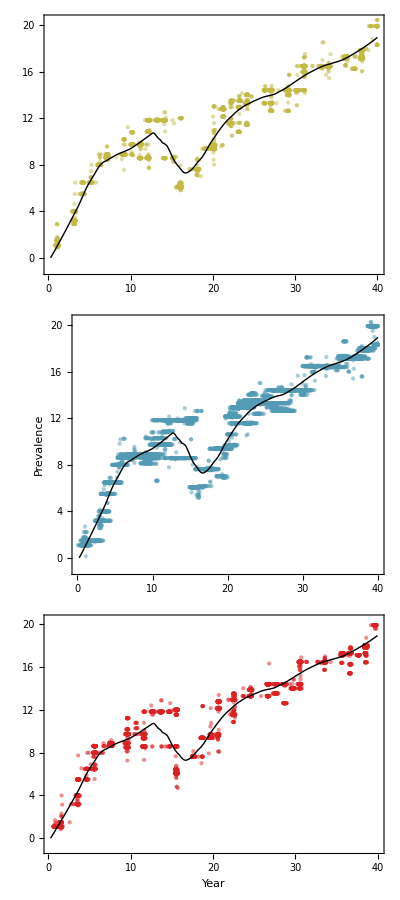

```mathematica
fig=Grid[Table[{Show[ListPlot[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]],PlotStyle->Directive[i/.spatialColorRules,Opacity[0.5]],PlotRange->{-1,max},ImagePadding->{{30,5},{If[i==2,25,10],5}},AspectRatio->0.5,FrameLabel->{If[i==2,"Year",""],If[i==1,"Prevalence",""]},ImageSize->400],ListLinePlot[loessList,PlotStyle->Directive[Black,Thick]]]},{i,0,demeCount-1}]]
```

```mathematica
Export["tipsSplineDistance.pdf",fig,"PDF"]
```

tipsSplineDistance.pdf

```mathematica
distance[list_]:=Module[{nf},
nf=Nearest[loessList[[All,1]]->loessList[[All,2]]];
Map[#[[2]]-First[nf[#[[1]]]]&,list]
]
```

```mathematica
Mean[distance[data]]
```

0.00614539

```mathematica
standardError[list_]:=StandardDeviation[list]/Sqrt[Length[list]]
```

```mathematica
standardError[distance[data]]
```

0.00546158

```mathematica
spatialDists=Table[With[{dist=distance[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]]]},{Mean[dist]-standardError[dist],Mean[dist],Mean[dist]+standardError[dist]}],{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[spatialDists,0.001],TableHeadings->{demes,{"95% lower","mean","95% upper"}}]
```

| 95% lower | mean | 95% upper
North | -0.087 | -0.079 | -0.071
Tropics | 0.126 | 0.136 | 0.146
South | -0.047 | -0.038 | -0.028

```mathematica
chart=MapIndexed[{GrayLevel[0.3],Line[{{#1[[1]],demeCount-#2[[1]]},{#1[[3]],demeCount-#2[[1]]}}],Line[{{#1[[1]],demeCount-#2[[1]]+0.1},{#1[[1]],demeCount-#2[[1]]-0.1}}],Line[{{#1[[3]],demeCount-#2[[1]]+0.1},{#1[[3]],demeCount-#2[[1]]-0.1}}],PointSize[0.03],spatialColors[[#2[[1]]]],Point[{#1[[2]],demeCount-#2[[1]]}]}&,spatialDists];
```

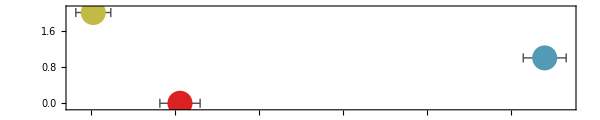

```mathematica
fig=Graphics[chart,AspectRatio->0.2,PlotRange->All,Frame->{True,False,True,False},PlotRangePadding->{{0,0},{0.5,0.5}},FrameLabel->{"Distance to AG spline"}]
```

```mathematica
Export["distAGSpatial.pdf",fig,"PDF"]
```

distAGSpatial.pdf

## Trees

First node is child, second is parent

```mathematica
branchScale=0.001;tipScale=0.001;clip=0.005;
```

```mathematica
getThickness[count_]:=Thickness[Clip[branchScale*N[Sqrt[count]],{0,clip}]]
```

```mathematica
getPointSize[count_]:=PointSize[N[tipScale*Sqrt[count]]];
```

```mathematica
name=1;year=2;trunk=3;loc=4;layout=5;ag1=6;ag2=7;
```

```mathematica
branchData=ToExpression[Import["out.branches","Table"]];
```

```mathematica
branchData[[1]]
```

{{49cda7e7,0.0548,1,1,17.9099,0.,0.},{5eb10190,0.,1,0,17.9099,0.,0.},625}

```mathematica
branchData[[1,{1,2},{year,layout}]]
```

{{0.0548,17.9099},{0.,17.9099}}

```mathematica
Length[branchData]
```

12820

### Analysis window

```mathematica
branchData=Select[branchData,(#[[1,year]]>clipStartTime&&#[[1,year]]<clipEndTime&&#[[2,year]]>clipStartTime&&#[[2,year]]<clipEndTime&)];
```

### Rotation

```mathematica
length=Length[branchData[[All,1,year]]];
```

```mathematica
times=Join[branchData[[All,1,year]],branchData[[All,2,year]]];
```

```mathematica
pc=PrincipalComponents[Join[branchData[[All,1,{ag1,ag2}]],branchData[[All,2,{ag1,ag2}]]]];
```

```mathematica
first=pc[[First[Ordering[times]]]];
```

```mathematica
last=pc[[Last[Ordering[times]]]];
```

```mathematica
pc=If[first[[1]]>last[[1]],Map[{-#[[1]],#[[2]]}&,pc],pc];
```

```mathematica
pc=Transpose[{pc[[1;;length]],pc[[length+1;;-1]]}];
```

```mathematica
branchData=MapThread[{{#1[[1,name]],#1[[1,year]],#1[[1,trunk]],#1[[1,loc]],#1[[1,layout]],#2[[1,1]],#2[[1,2]]},{#1[[2,name]],#1[[2,year]],#1[[2,trunk]],#1[[2,loc]],#1[[2,layout]],#2[[2,1]],#2[[2,2]]},#1[[3]]}&,{branchData,pc}];
```

```mathematica
startingPoint=If[first[[1]]>last[[1]],last,first];
```

```mathematica
dist[coord_]:=EuclideanDistance[startingPoint,coord]
```

### Time vs Layout

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

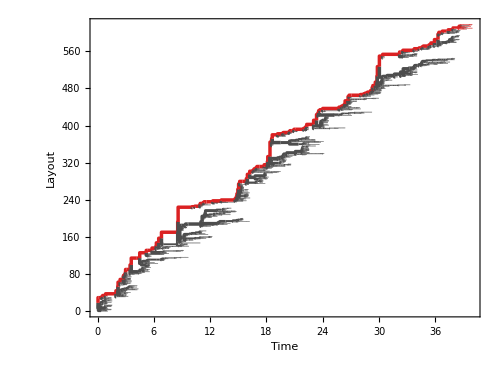

```mathematica
fig=Graphics[branchLines,AspectRatio->0.75,ImageSize->500,PlotRange->All,FrameLabel->{"Time","Layout"},Frame->{True,False,False,False}]
```

```mathematica
Export["tree.pdf",fig,"PDF"]
```

tree.pdf

### Time vs Layout - clusters

```mathematica
branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

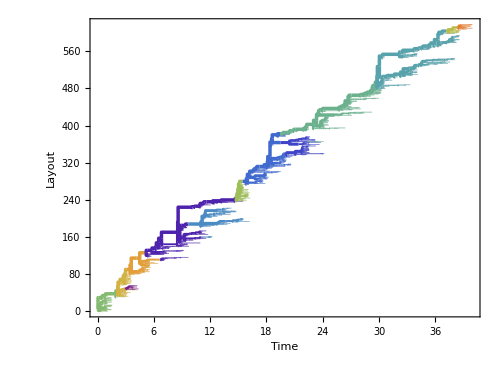

```mathematica
fig=Graphics[branchLines,AspectRatio->0.75,PlotRange->All,ImageSize->500,FrameLabel->{"Time","Layout"},Frame->{True,False,False,False}]
```

```mathematica
Export["treeClusters.pdf",fig,"PDF"]
```

treeClusters.pdf

### Time vs Layout with location

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

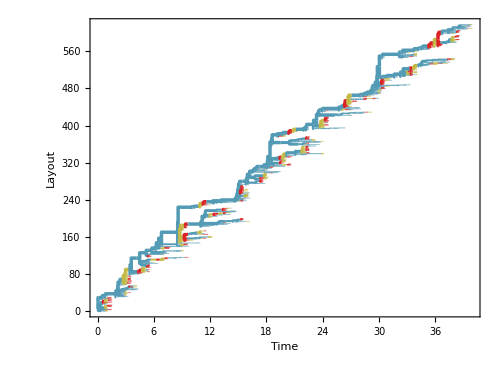

```mathematica
fig=Graphics[branchLines,AspectRatio->0.75,PlotRange->All,ImageSize->500,FrameLabel->{"Time","Layout"},Frame->{True,False,False,False}]
```

```mathematica
Export["treeSpatial.pdf",fig,"PDF"]
```

treeSpatial.pdf

### AG1 vs AG2

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tallies=Tally[Join[branchData[[All,1,{ag1,ag2}]],branchData[[All,2,{ag1,ag2}]]]];
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],0/.trunkColorRules,Point[#[[1]]]}&,tallies];
```

```mathematica
tipPoints={Opacity[1],tipPoints};
```

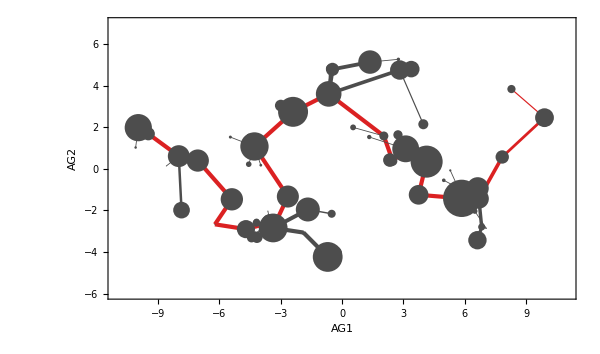

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG1","AG2"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeAG1AG2.pdf",fig,"PDF"]
```

treeAG1AG2.pdf

### AG1 vs AG2 with clusters

```mathematica
branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,branchData];
```

```mathematica
branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}],clusterColors[[clusterFunction[#[[2,{ag1,ag2}]]]]],Line[{Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}],#[[2,{ag1,ag2}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tallies=Tally[Join[branchData[[All,1,{ag1,ag2}]],branchData[[All,2,{ag1,ag2}]]]];
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],clusterColors[[clusterFunction[#[[1]]]]],Point[#[[1]]]}&,tallies];
```

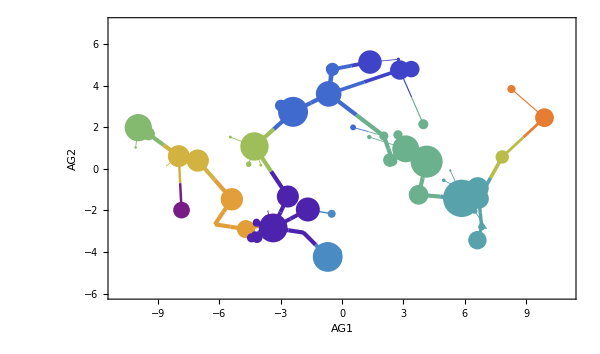

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeAG1AG2Clusters.pdf",fig,"PDF"]
```

treeAG1AG2Cluster.pdf

## Mutation statistics

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&&#[[1,year]]<endTime-1&)];
```

```mathematica
sideBranches=Select[branchData,(#[[1,trunk]]==0&&#[[1,year]]<endTime-1&)];
```

### Mutation rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,sideBranches]];
```

```mathematica
trunkMutationRate=trunkCount/trunkOpportunity
```

0.539471

```mathematica
sideBranchMutationRate=sideBranchCount/sideBranchOpportunity
```

0.157882

### Antigenic flux

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches]];
```

```mathematica
sideBranchDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches]];
```

```mathematica
trunkFluxRate=trunkDistance/trunkOpportunity
```

0.884907

```mathematica
sideBranchFluxRate=sideBranchDistance/sideBranchOpportunity
```

0.136277

### Mutation size

```mathematica
trunkMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches],#>0.0000001&];
```

```mathematica
sideBranchMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches],#>0.0000001&];
```

```mathematica
trunkMutationSize=Mean[trunkMutations]
```

1.64032

```mathematica
sideBranchMutationSize=Mean[sideBranchMutations]
```

0.863158

```mathematica
TableForm[Round[{{sideBranchMutationRate,sideBranchMutationSize,sideBranchFluxRate},{trunkMutationRate,trunkMutationSize,trunkFluxRate}},0.001],TableHeadings->{{"Side branches","Trunk branches"},{"Mutation rate","Mutation size","Antigenic flux"}}]
```

| Mutation rate | Mutation size | Antigenic flux
Side branches | 0.158 | 0.863 | 0.136
Trunk branches | 0.539 | 1.64 | 0.885

```mathematica
365*0.00028
```

0.1022

### Mutation spectrum

Forward movement

```mathematica
sideBranchMutations1D=Select[Map[#[[1,ag1]]-#[[2,ag1]]&,sideBranches],(#≠0&)];
```

```mathematica
trunkMutations1D=Select[Map[#[[1,ag1]]-#[[2,ag1]]&,trunkBranches],(#≠0&)];
```

```mathematica
Mean[sideBranchMutations1D]
```

0.0314024

```mathematica
Mean[trunkMutations1D]
```

0.863436

```mathematica
comparisonHistogram[list_,col_]:=Histogram[list,{0.25},"PDF",PlotRange->{{-4,4},{0,1}},ChartStyle->Directive[EdgeForm[Thin],col],ImageSize->300,Axes->False,Frame->{True,True,False,False}];
```

```mathematica
sideBranchMutations2D=Select[Map[#[[1,{ag1,ag2}]]-#[[2,{ag1,ag2}]]&,sideBranches],(#[[1]]≠0&&#[[2]]≠0&)];
```

```mathematica
trunkMutations2D=Select[Map[#[[1,{ag1,ag2}]]-#[[2,{ag1,ag2}]]&,trunkBranches],(#[[1]]≠0&&#[[2]]≠0&)];
```

```mathematica
comparisonDensityHistogram[list_,col_]:=SmoothDensityHistogram[list,0.5,ColorFunction->(Blend[{White,col},#]&),Mesh->20,PlotRange->{{-4,4},{-3.5,3.5}},AspectRatio->Automatic,ImageSize->300,Frame->{True,True,False,False},Axes->True,AxesStyle->Dashed]
```

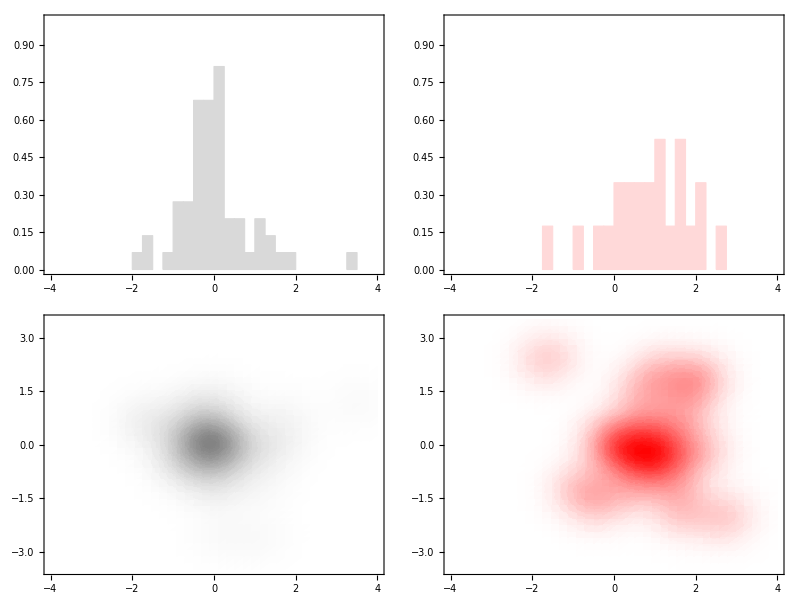

```mathematica
fig=Grid[{{comparisonHistogram[sideBranchMutations1D,LightGray],comparisonHistogram[trunkMutations1D,LightRed]},{comparisonDensityHistogram[sideBranchMutations2D,Gray],comparisonDensityHistogram[trunkMutations2D,Red]}},Spacings->{1,1}]
```

```mathematica
Export["mutationSpectrum.pdf",fig,"PDF"]
```

mutationSpectrum.pdf

## Migration statistics

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&&#[[1,year]]<endTime-1&)];
```

```mathematica
sideBranches=Select[branchData,(#[[1,trunk]]==0&&#[[1,year]]<endTime-1&)];
```

### Proportion of each deme in trunk

```mathematica
trunkLengths=Table[Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,Select[trunkBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)]]],{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[trunkLengths/Total[trunkLengths],0.001],TableHeadings->{demes}]
```

North | 0.05
Tropics | 0.9
South | 0.05

### Migration rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,sideBranches]];
```

```mathematica
trunkRate=trunkCount/trunkOpportunity
```

0.392342

```mathematica
sideBranchRate=sideBranchCount/sideBranchOpportunity
```

0.631529

### Migration spectrum

```mathematica
trunkCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkRates=(trunkCounts/trunkOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[Round[trunkRates,0.001]/.(0.->""),TableHeadings->{demes,demes}]
```

| North | Tropics | South
North |  | 2.15 | 1.075
Tropics | 0.06 |  | 0.089
South | 1.608 | 1.072 |

```mathematica
sideBranchCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchRates=(sideBranchCounts/sideBranchOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[Round[sideBranchRates,0.001]/.(0.->""),TableHeadings->{demes,demes}]
```

| North | Tropics | South
North |  | 0.236 | 0.707
Tropics | 0.295 |  | 0.205
South | 0.568 | 0.213 |

### Seasonal migration spectrum

```mathematica
seasonalMigRate[branches_,start_,stop_]:=Module[{goodBranches,opportunities,counts},
goodBranches=Select[branches,(FractionalPart[#[[1,year]]]<stop&&FractionalPart[#[[2,year]]]≥start)&];
opportunities=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,goodBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
counts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,goodBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
(counts/opportunities)*(1-DiagonalMatrix[Table[1,{demeCount}]])
]
```

```mathematica
Grid[Table[{TableForm[Round[seasonalMigRate[branchData,i,i+0.25],0.001],TableHeadings->{demes,demes}]},{i,0,0.75,0.25}],Spacings->{2,2}]
```

| North | Tropics | South
North | 0. | 0.414 | 0.776
Tropics | 0.06 | 0. | 0.06
South | 0.433 | 0. | 0.
 | North | Tropics | South
North | 0. | 0.264 | 1.41
Tropics | 0.014 | 0. | 0.461
South | 0.03 | 0.119 | 0.
 | North | Tropics | South
North | 0. | 0.084 | 0.084
Tropics | 0.106 | 0. | 0.026
South | 0.917 | 0.48 | 0.
 | North | Tropics | South
North | 0. | 0.045 | 0.
Tropics | 0.703 | 0. | 0.
South | 13.183 | 0.824 | 0.

### Mutation rate - spatial

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
count=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0,1,0]&,branches]];
rate=count/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[rates,0.001],TableHeadings->{demes}]
```

North | 0.19
Tropics | 0.23
South | 0.138

### Antigenic flux - spatial

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
rate=antigenicDistance/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[rates,0.001],TableHeadings->{demes}]
```

North | 0.175
Tropics | 0.267
South | 0.113

### Antigenic flux - spatial - absolute

```mathematica
rates=Table[
branches=Select[branchData,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
antigenicDistance,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[rates,0.001],TableHeadings->{demes}]
```

North | 13.825
Tropics | 66.28
South | 8.168

## Animation

```mathematica
tLines[time_]:=Module[{data,branchLines},
data=Select[branchData,(#[[1,year]]<time&&#[[2,year]]<time&)];branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,data];
{CapForm["Round"],branchLines}]
```

```mathematica
tPoints[time_]:=Module[{data,tallies,tipPoints},
data=Select[branchData,(#[[1,year]]<time&&#[[2,year]]<time&)];
tallies=Tally[Join[data[[All,1,{ag1,ag2}]],data[[All,2,{ag1,ag2}]]]];
tipPoints=Map[{getPointSize[#[[2]]],clusterColors[[clusterFunction[#[[1]]]]],Point[#[[1]]]}&,tallies];
tipPoints
]
```

```mathematica
frame[time_]:=Graphics[{tLines[time],tPoints[time]},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG1","AG2"},Frame->{True,True,False,False},ImageSize->1000]
```

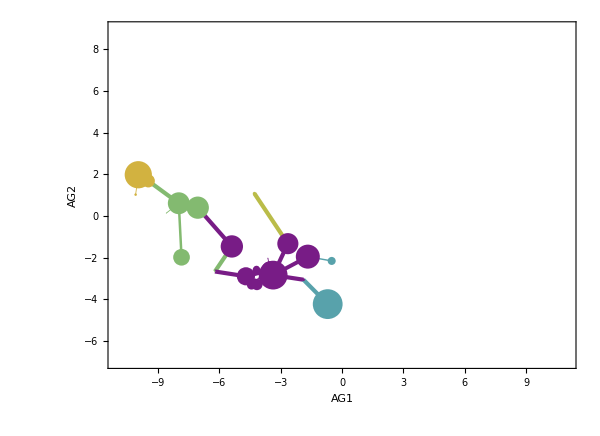

```mathematica
frame[15]
```

Do[f = frame[i]; Export["frames/" <> ToString[IntegerPart[i*10]] <> ".jpg", f, "JPG"];, {i, startTime, endTime, 0.1}]